```mathematica
(*
operators_and_bases_scratch.nb
A scratch notebook to hash out the definitions of the bases of the ground state of Rb-87 and the operators which act upon them.
*)
```

```mathematica
(*
The order of the components is as follows for the coupled and uncoupled bases, respectively:
ind: |F, m_F>
1: |2,2>
2: |2,1>
3: |2,0>
4: |2,-1>
5: |2,-2>
6: |1,1>
7: |1,0>
8: |1,-1>

ind: |I=3/2, J=1/2, m_I, m_J>
1: |3/2, 1/2>
2: |3/2, -1/2>
3: |1/2, 1/2>
4: |1/2, -1/2>
5: |-1/2, 1/2>
6: |-1/2, -1/2>
7: |-3/2, 1/2>
8: |-3/2, -1/2>
*)
```

```mathematica
(* Send to the right directory if necessary *)
(* the main project directory sits one above this subproject directory, i.e. at the -2 position. *)
projectDirectory=FileNameTake[NotebookDirectory[],{1,-2}]
packageDirectory=FileNameJoin@{projectDirectory,"mathematica_packages\\"}
outputDirectory=FileNameJoin@{projectDirectory,"output\\"}

If[Not@MemberQ[$Path,packageDirectory],
AppendTo[$Path,packageDirectory];
]

Get["RbGroundStateAlgebra.m"]
Get["BatesConstants.m"]
```

C:\Users\josep\forschung\modeling\bubble_bec

C:\Users\josep\forschung\modeling\bubble_bec\mathematica_packages

C:\Users\josep\forschung\modeling\bubble_bec\output

## Looking at, verifying vectors and operators

## moving between bases

```mathematica
Dimensions/@{fInds,ijInds}
```

{{8,2},{8,2}}

```mathematica
Total[#^2]&/@uftoij (* Check that each row is normalized *)
```

{1,1,1,1,1,1,1,1}

```mathematica
Dimensions@uftoij (* Check that the dimensions are right *)
```

{8,8}

```mathematica
uftoij.{1,0,0,0,0,0,0,0}
```

{1,0,0,0,0,0,0,0}

```mathematica
uftoij.{0,0,0,0,0,0,0,1}
```

{0,0,0,0,0,-1/2,(√3)/2,0}

```mathematica
uftoij//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 | 0 | 0 | 0 | (√3)/2 | 0 | 0
0 | (√3)/2 | 0 | 0 | 0 | -1/2 | 0 | 0
0 | 0 | 1/(√2) | 0 | 0 | 0 | 1/(√2) | 0
0 | 0 | 1/(√2) | 0 | 0 | 0 | -1/(√2) | 0
0 | 0 | 0 | -(√3)/2 | 0 | 0 | 0 | -1/2
0 | 0 | 0 | -1/2 | 0 | 0 | 0 | (√3)/2
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0)

## nuclear spin (I) operators

```mathematica
ipij//MatrixForm
```

(0 | 0 | √3 ℏ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | √3 ℏ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 ℏ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2 ℏ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | √3 ℏ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | √3 ℏ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
ipij.{0,0,1,0,0,0,0,0}
```

{√3 ℏ,0,0,0,0,0,0,0}

```mathematica
imij//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
√3 ℏ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | √3 ℏ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 ℏ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 ℏ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | √3 ℏ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | √3 ℏ | 0 | 0)

```mathematica
ixij//MatrixForm
```

(0 | 0 | (√3 ℏ)/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (√3 ℏ)/2 | 0 | 0 | 0 | 0
(√3 ℏ)/2 | 0 | 0 | 0 | ℏ | 0 | 0 | 0
0 | (√3 ℏ)/2 | 0 | 0 | 0 | ℏ | 0 | 0
0 | 0 | ℏ | 0 | 0 | 0 | (√3 ℏ)/2 | 0
0 | 0 | 0 | ℏ | 0 | 0 | 0 | (√3 ℏ)/2
0 | 0 | 0 | 0 | (√3 ℏ)/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | (√3 ℏ)/2 | 0 | 0)

```mathematica
(* agrees with manual calculations *)
ixf/(ℏ/4)//MatrixForm
```

(0 | 3 | 0 | 0 | 0 | -√3 | 0 | 0
3 | 0 | 3 √(3/2) | 0 | 0 | 0 | -√(3/2) | 0
0 | 3 √(3/2) | 0 | -3 √(3/2) | 0 | 1/(√2) | 0 | 1/(√2)
0 | 0 | -3 √(3/2) | 0 | 3 | 0 | -√(3/2) | 0
0 | 0 | 0 | 3 | 0 | 0 | 0 | √3
-√3 | 0 | 1/(√2) | 0 | 0 | 0 | 5/(√2) | 0
0 | -√(3/2) | 0 | -√(3/2) | 0 | 5/(√2) | 0 | -5/(√2)
0 | 0 | 1/(√2) | 0 | √3 | 0 | -5/(√2) | 0)

```mathematica
(iyij)//MatrixForm
```

(0 | 0 | -1/2 ⅈ √3 ℏ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1/2 ⅈ √3 ℏ | 0 | 0 | 0 | 0
1/2 ⅈ √3 ℏ | 0 | 0 | 0 | -ⅈ ℏ | 0 | 0 | 0
0 | 1/2 ⅈ √3 ℏ | 0 | 0 | 0 | -ⅈ ℏ | 0 | 0
0 | 0 | ⅈ ℏ | 0 | 0 | 0 | -1/2 ⅈ √3 ℏ | 0
0 | 0 | 0 | ⅈ ℏ | 0 | 0 | 0 | -1/2 ⅈ √3 ℏ
0 | 0 | 0 | 0 | 1/2 ⅈ √3 ℏ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/2 ⅈ √3 ℏ | 0 | 0)

```mathematica
iyf/(ℏ/4)//MatrixForm
```

(0 | -3 ⅈ | 0 | 0 | 0 | ⅈ √3 | 0 | 0
3 ⅈ | 0 | -3 ⅈ √(3/2) | 0 | 0 | 0 | ⅈ √(3/2) | 0
0 | 3 ⅈ √(3/2) | 0 | 3 ⅈ √(3/2) | 0 | ⅈ/(√2) | 0 | -ⅈ/(√2)
0 | 0 | -3 ⅈ √(3/2) | 0 | -3 ⅈ | 0 | -ⅈ √(3/2) | 0
0 | 0 | 0 | 3 ⅈ | 0 | 0 | 0 | ⅈ √3
-ⅈ √3 | 0 | -ⅈ/(√2) | 0 | 0 | 0 | -(5 ⅈ)/(√2) | 0
0 | -ⅈ √(3/2) | 0 | ⅈ √(3/2) | 0 | (5 ⅈ)/(√2) | 0 | (5 ⅈ)/(√2)
0 | 0 | ⅈ/(√2) | 0 | -ⅈ √3 | 0 | -(5 ⅈ)/(√2) | 0)

```mathematica
izij//MatrixForm
```

((3 ℏ)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (3 ℏ)/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ℏ/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ℏ/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ℏ/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ℏ/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -(3 ℏ)/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -(3 ℏ)/2)

```mathematica
(izf/(ℏ/2))//MatrixForm
(* This matches the manual calculation from 30 Aug. '18 (MSNB#7) *)
```

(3 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 3/2 | 0 | 0 | 0 | (√3)/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | -3/2 | 0 | 0 | 0 | (√3)/2
0 | 0 | 0 | 0 | -3 | 0 | 0 | 0
0 | (√3)/2 | 0 | 0 | 0 | 5/2 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (√3)/2 | 0 | 0 | 0 | -5/2)

```mathematica
ℏ
```

ℏ

```mathematica
(izij.izij+ixij.ixij+iyij.iyij)//MatrixForm
(* Should be ℏ^2*(3/2)(3/2+1)*Identity *)
```

((15 ℏ^2)/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (15 ℏ^2)/4 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (15 ℏ^2)/4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (15 ℏ^2)/4 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (15 ℏ^2)/4 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | (15 ℏ^2)/4 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | (15 ℏ^2)/4 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | (15 ℏ^2)/4)

```mathematica
(izf.izf+ixf.ixf+iyf.iyf)//MatrixForm
```

((15 ℏ^2)/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (15 ℏ^2)/4 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (15 ℏ^2)/4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (15 ℏ^2)/4 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (15 ℏ^2)/4 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | (15 ℏ^2)/4 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | (15 ℏ^2)/4 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | (15 ℏ^2)/4)

## net electronic angular momentum (J) operators

```mathematica
jpij//MatrixForm
```

(0 | ℏ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ℏ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ℏ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ℏ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
jpij.SparseArray[{{#}->1},{8}]&/@Range[8] (* SparseArray[{{#}->1,{8}] constructs a list of length 8 where the #th element is set to 1 and the rest are 0. It is a compact way of creating the #th unit vector. *)
```

{{0,0,0,0,0,0,0,0},{ℏ,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,ℏ,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,ℏ,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,ℏ,0}}

```mathematica
jmij//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ℏ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ℏ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ℏ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | ℏ | 0)

```mathematica
jmij.SparseArray[{{#}->1},{8}]&/@Range[8]
```

{{0,ℏ,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,ℏ,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,ℏ,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,ℏ},{0,0,0,0,0,0,0,0}}

```mathematica
(jxij/(ℏ/2))//MatrixForm
(jxf/(ℏ/4))//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

(0 | 1 | 0 | 0 | 0 | √3 | 0 | 0
1 | 0 | √(3/2) | 0 | 0 | 0 | √(3/2) | 0
0 | √(3/2) | 0 | -√(3/2) | 0 | -1/(√2) | 0 | -1/(√2)
0 | 0 | -√(3/2) | 0 | 1 | 0 | √(3/2) | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | -√3
√3 | 0 | -1/(√2) | 0 | 0 | 0 | -1/(√2) | 0
0 | √(3/2) | 0 | √(3/2) | 0 | -1/(√2) | 0 | 1/(√2)
0 | 0 | -1/(√2) | 0 | -√3 | 0 | 1/(√2) | 0)

```mathematica
(jyij/(ℏ/2))//MatrixForm
(jyf/(ℏ/4))//MatrixForm
```

(0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0)

(0 | -ⅈ | 0 | 0 | 0 | -ⅈ √3 | 0 | 0
ⅈ | 0 | -ⅈ √(3/2) | 0 | 0 | 0 | -ⅈ √(3/2) | 0
0 | ⅈ √(3/2) | 0 | ⅈ √(3/2) | 0 | -ⅈ/(√2) | 0 | ⅈ/(√2)
0 | 0 | -ⅈ √(3/2) | 0 | -ⅈ | 0 | ⅈ √(3/2) | 0
0 | 0 | 0 | ⅈ | 0 | 0 | 0 | -ⅈ √3
ⅈ √3 | 0 | ⅈ/(√2) | 0 | 0 | 0 | ⅈ/(√2) | 0
0 | ⅈ √(3/2) | 0 | -ⅈ √(3/2) | 0 | -ⅈ/(√2) | 0 | -ⅈ/(√2)
0 | 0 | -ⅈ/(√2) | 0 | ⅈ √3 | 0 | ⅈ/(√2) | 0)

```mathematica
jzij/(ℏ/2)//MatrixForm
jzf/(ℏ/2)//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 | 0 | 0 | 0 | -(√3)/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | -1/2 | 0 | 0 | 0 | -(√3)/2
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | -(√3)/2 | 0 | 0 | 0 | -1/2 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -(√3)/2 | 0 | 0 | 0 | 1/2)

## net atomic angular momentum (F) operators

```mathematica
fzf/ℏ//MatrixForm (* The only non-zero elements should be the mF values along the diagonal. *)
fzij/ℏ//MatrixForm
```

(2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

(2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -2)

```mathematica
fxf/ℏ//MatrixForm
fxij/ℏ//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | √(3/2) | 0 | 0 | 0 | 0 | 0
0 | √(3/2) | 0 | -√(3/2) | 0 | 0 | 0 | 0
0 | 0 | -√(3/2) | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/(√2) | 0
0 | 0 | 0 | 0 | 0 | 1/(√2) | 0 | -1/(√2)
0 | 0 | 0 | 0 | 0 | 0 | -1/(√2) | 0)

(0 | 1/2 | (√3)/2 | 0 | 0 | 0 | 0 | 0
1/2 | 0 | 0 | (√3)/2 | 0 | 0 | 0 | 0
(√3)/2 | 0 | 0 | 1/2 | 1 | 0 | 0 | 0
0 | (√3)/2 | 1/2 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 1/2 | (√3)/2 | 0
0 | 0 | 0 | 1 | 1/2 | 0 | 0 | (√3)/2
0 | 0 | 0 | 0 | (√3)/2 | 0 | 0 | 1/2
0 | 0 | 0 | 0 | 0 | (√3)/2 | 1/2 | 0)

```mathematica
fyf/ℏ//MatrixForm
fyij/ℏ//MatrixForm
```

(0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | -ⅈ √(3/2) | 0 | 0 | 0 | 0 | 0
0 | ⅈ √(3/2) | 0 | ⅈ √(3/2) | 0 | 0 | 0 | 0
0 | 0 | -ⅈ √(3/2) | 0 | -ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/(√2) | 0
0 | 0 | 0 | 0 | 0 | ⅈ/(√2) | 0 | ⅈ/(√2)
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/(√2) | 0)

(0 | -ⅈ/2 | -(ⅈ √3)/2 | 0 | 0 | 0 | 0 | 0
ⅈ/2 | 0 | 0 | -(ⅈ √3)/2 | 0 | 0 | 0 | 0
(ⅈ √3)/2 | 0 | 0 | -ⅈ/2 | -ⅈ | 0 | 0 | 0
0 | (ⅈ √3)/2 | ⅈ/2 | 0 | 0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0 | 0 | -ⅈ/2 | -(ⅈ √3)/2 | 0
0 | 0 | 0 | ⅈ | ⅈ/2 | 0 | 0 | -(ⅈ √3)/2
0 | 0 | 0 | 0 | (ⅈ √3)/2 | 0 | 0 | -ⅈ/2
0 | 0 | 0 | 0 | 0 | (ⅈ √3)/2 | ⅈ/2 | 0)

```mathematica
fpf/ℏ//MatrixForm
fmf/ℏ//MatrixForm
```

(0 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | √6 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -√6 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | √2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -√2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | √6 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -√6 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | √2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -√2 | 0)

## Using operators

## I·J coupling

```mathematica
(ixf.jxf+iyf.jyf+izf.jzf)/(ℏ/2)^2//MatrixForm
```

(3 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 3 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 3 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -5 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -5 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -5)

```mathematica
(ixij.jxij+iyij.jyij+izij.jzij)/(ℏ/2)^2//MatrixForm
```

(3 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -3 | 2 √3 | 0 | 0 | 0 | 0 | 0
0 | 2 √3 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 4 | 0 | 0 | 0
0 | 0 | 0 | 4 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 2 √3 | 0
0 | 0 | 0 | 0 | 0 | 2 √3 | -3 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 3)

## Toy Hamiltonians

```mathematica
{1,0,0,0,0,0,0,0}.(bx*jxf+by*jyf).{0,0,0,0,0,1,0,0}
```

1/4 √3 bx ℏ-1/4 ⅈ √3 by ℏ

```mathematica
SparseArray[{{1}->1},{8}].jp1f.SparseArray[{{6}->1},{8}]
```

-1/2 √(3/2) ℏ

```mathematica
SparseArray[{{1}->1},{8}].jm1f.SparseArray[{{6}->1},{8}]
```

0

```mathematica
hintTemp=Subscript[μ, B]/ℏ*(gJ*jp1f+gI*ip1f);
```

```mathematica
SparseArray[{{1}->1},{8}].hintTemp.SparseArray[{{6}->1},{8}]
```

((-0.000609397 ℏ-1/2 √(3/2) gJ ℏ) μ_B)/ℏ

```mathematica
Simplify@%
```

(-0.000609397-0.612372 gJ) μ_B

```mathematica
(* THE ABOVE AGREES WITH MY MANUAL CALCULATIONS (Murphree Bates Science Notebook #2 pp.88--96) *)
```

```mathematica
(* Set gI to zero (it's ~0.001*gJ) and multiply out common factors to get a better look at the relative strengths of the transitions. *)
Simplify@(2*Sqrt[2]*hintTemp/(gJ*Subscript[μ, B])/.{gI->0})//MatrixForm
```

(0. | -1.+0.00298542/gJ | 0. | 0. | 0. | -1.73205-0.00172364/gJ | 0. | 0.
0. | 0. | -1.22474+0.00365638/gJ | 0. | 0. | 0. | -1.22474-0.00121879/gJ | 0.
0. | 0. | 0. | 1.22474-0.00365638/gJ | 0. | 0. | 0. | 0.707107+0.000703671/gJ
0. | 0. | 0. | 0. | -1.+0.00298542/gJ | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.707107+0.000703671/gJ | 0. | 0. | 0. | 0.707107+0.00351836/gJ | 0.
0. | 0. | 0. | -1.22474-0.00121879/gJ | 0. | 0. | 0. | -0.707107-0.00351836/gJ
0. | 0. | 0. | 0. | 1.73205+0.00172364/gJ | 0. | 0. | 0.)

## Breit-Rabi

```mathematica
(hamBR=(a/ℏ^2)*(ixf.jxf+iyf.jyf+izf.jzf)+(μB/ℏ)*(gJ*jzf+gi*izf)*bmag)//Simplify//MatrixForm
```

(1/4 (3 a+2 bmag (3 gi+gJ) μB) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/4 (3 a+bmag (3 gi+gJ) μB) | 0 | 0 | 0 | 1/4 √3 bmag (gi-gJ) μB | 0 | 0
0 | 0 | (3 a)/4 | 0 | 0 | 0 | 1/2 bmag (gi-gJ) μB | 0
0 | 0 | 0 | 1/4 (3 a-bmag (3 gi+gJ) μB) | 0 | 0 | 0 | 1/4 √3 bmag (gi-gJ) μB
0 | 0 | 0 | 0 | 1/4 (3 a-2 bmag (3 gi+gJ) μB) | 0 | 0 | 0
0 | 1/4 √3 bmag (gi-gJ) μB | 0 | 0 | 0 | 1/4 (-5 a+bmag (5 gi-gJ) μB) | 0 | 0
0 | 0 | 1/2 bmag (gi-gJ) μB | 0 | 0 | 0 | -(5 a)/4 | 0
0 | 0 | 0 | 1/4 √3 bmag (gi-gJ) μB | 0 | 0 | 0 | 1/4 (-5 a+bmag (-5 gi+gJ) μB))

```mathematica
eigsys=Eigensystem[hamBR](* {values, vectors} *)
```

{{1/4 (3 a-6 bmag gi μB-2 bmag gJ μB),1/4 (3 a+6 bmag gi μB+2 bmag gJ μB),1/4 (-a+2 √(4 a^2+bmag^2 gi^2 μB^2-2 bmag^2 gi gJ μB^2+bmag^2 gJ^2 μB^2)),1/4 (-a-2 √(4 a^2+bmag^2 gi^2 μB^2-2 bmag^2 gi gJ μB^2+bmag^2 gJ^2 μB^2)),1/4 (-a-4 bmag gi μB+2 √(4 a^2+2 a bmag gi μB-2 a bmag gJ μB+bmag^2 gi^2 μB^2-2 bmag^2 gi gJ μB^2+bmag^2 gJ^2 μB^2)),1/4 (-a-4 bmag gi μB-2 √(4 a^2+2 a bmag gi μB-2 a bmag gJ μB+bmag^2 gi^2 μB^2-2 bmag^2 gi gJ μB^2+bmag^2 gJ^2 μB^2)),1/4 (-a+4 bmag gi μB-2 √(4 a^2-2 a bmag gi μB+2 a bmag gJ μB+bmag^2 gi^2 μB^2-2 bmag^2 gi gJ μB^2+bmag^2 gJ^2 μB^2)),1/4 (-a+4 bmag gi μB+2 √(4 a^2-2 a bmag gi μB+2 a bmag gJ μB+bmag^2 gi^2 μB^2-2 bmag^2 gi gJ μB^2+bmag^2 gJ^2 μB^2))},{{0,0,0,0,1,0,0,0},{1,0,0,0,0,0,0,0},{0,0,-(-2 a-√(4 a^2+bmag^2 gi^2 μB^2-2 bmag^2 gi gJ μB^2+bmag^2 gJ^2 μB^2))/(bmag (gi-gJ) μB),0,0,0,1,0},{0,0,-(-2 a+√(4 a^2+bmag^2 gi^2 μB^2-2 bmag^2 gi gJ μB^2+bmag^2 gJ^2 μB^2))/(bmag (gi-gJ) μB),0,0,0,1,0},{0,0,0,(4 a+bmag gi μB-bmag gJ μB+2 √(4 a^2+2 a bmag gi μB-2 a bmag gJ μB+bmag^2 gi^2 μB^2-2 bmag^2 gi gJ μB^2+bmag^2 gJ^2 μB^2))/(√3 bmag (gi-gJ) μB),0,0,0,1},{0,0,0,(4 a+bmag gi μB-bmag gJ μB-2 √(4 a^2+2 a bmag gi μB-2 a bmag gJ μB+bmag^2 gi^2 μB^2-2 bmag^2 gi gJ μB^2+bmag^2 gJ^2 μB^2))/(√3 bmag (gi-gJ) μB),0,0,0,1},{0,-(-4 a+bmag gi μB-bmag gJ μB+2 √(4 a^2-2 a bmag gi μB+2 a bmag gJ μB+bmag^2 gi^2 μB^2-2 bmag^2 gi gJ μB^2+bmag^2 gJ^2 μB^2))/(√3 bmag (gi-gJ) μB),0,0,0,1,0,0},{0,-(-4 a+bmag gi μB-bmag gJ μB-2 √(4 a^2-2 a bmag gi μB+2 a bmag gJ μB+bmag^2 gi^2 μB^2-2 bmag^2 gi gJ μB^2+bmag^2 gJ^2 μB^2))/(√3 bmag (gi-gJ) μB),0,0,0,1,0,0}}}

```mathematica
Dimensions@eigsys
```

{2,8}

```mathematica
(* Create numerical expressions of the eigenvectors and eigenvalues. *)
numVals={μB->muB,ℏ->hbar,a->ahfsS12,gJ->gJS12,gi->gI};
evals[bmag_]:=Evaluate[eigsys[[1]]/.numVals];
evecsUnorm[bmag_]:=Evaluate[eigsys[[2]]/.numVals];
evecs[bmag_]:=(#/Sqrt[#.#])&/@evecsUnorm[bmag];
```

```mathematica
Abs@Round[evecs[0.001]]//MatrixForm
(* Look at each of the eigenvectors in a low magnitude magnetic field, where they should be mostly {F,mF} eigenstates. Rounding the components of each vector to the nearest integer (0 or plus/minus 1) and then taking the absolute value makes this manifest. *)
```

(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
(*loBInds={{2,-2},{2,2},{2,0},{1,0},{2,-1},{1,-1},{1,1},{2,1}}*)
loBInds=Abs@Round[evecs[0.001]].fInds
```

{{2,-2},{2,2},{2,0},{1,0},{2,-1},{1,-1},{1,1},{2,1}}

```mathematica
(Abs@Round[uftoij.#]&/@evecs[10])//MatrixForm
(* Looking at each of the eigenvectors in a high magnitude magnetic field, where they should be mostly {mI,mJ} eigenstates. However we have been working in the {F,mF} basis, so we apply a basis transformation to take it into the basis whose basis vectors are {mI,mJ} eigenstates. Then repeat the rounding and absolute value procedure applied to the low field states. *)
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0)

```mathematica
(*hiBInds={{-3/2,-1/2},{3/2,1/2},{-1/2,1/2},{1/2,-1/2},{-3/2,1/2},{-1/2,-1/2},{3/2,-1/2},{1/2,1/2}}*)
hiBInds=Abs[Round[uftoij.#]&/@evecs[10]].ijInds
```

{{-3/2,-1/2},{3/2,1/2},{-1/2,1/2},{1/2,-1/2},{-3/2,1/2},{-1/2,-1/2},{3/2,-1/2},{1/2,1/2}}

```mathematica
plotStateLabels=MapThread[TextString[#1]<>"->"<>TextString[#2]&,{loBInds,hiBInds}];
```

```mathematica
plots=MapThread[
Plot[#1/(h*10^9),{bmag,0,15000},
PlotRange->{-25,25},
(*PlotLegends->"test",*)
Frame->True,
PlotStyle->ColorData[97,"ColorList"][[#2]],
FrameLabel->{"B mag [G]","E/h [GHz]"},
PlotLabel->"Hyperfine sublevel energy splitting"]&,
{evals[bmag/10000],Range[8]}];
```

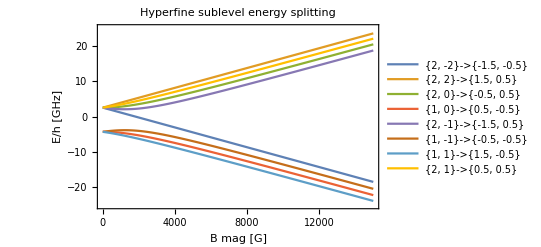

```mathematica
Legended[Show[plots],LineLegend[ColorData[97]/@Range[8],plotStateLabels]]
```

```mathematica
Block[{ind=8},
Print[TextString@loBInds[[ind]]];
Print[Simplify@eigsys[[1,ind]]];
];
```

{2, 1}

-a/4+bmag gi μB+1/2 √(4 a^2+2 a bmag (-gi+gJ) μB+bmag^2 (gi-gJ)^2 μB^2)

```mathematica
uftoij.SparseArray[{2}->1,{8}]
```

{0,1/2,(√3)/2,0,0,0,0,0}

```mathematica
ijInds[[{2,3}]]
```

{{3/2,-1/2},{1/2,1/2}}

```mathematica
(1+(#*0.23*7.9/3)^2)&/@Range[4]
```

{1.36683,2.46733,4.30149,6.86931}